## Demonstration to solve “Sphere Shell Theorem” which appears quite frequently in gravitational and electric field.

### Define the position vector 𝕣(r,θ,ϕ)

```mathematica
𝕣[r_,θ_,ϕ_]=r{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
```

```mathematica
𝕣[r,θ,ϕ]//MatrixForm
```

(r Cos[ϕ] Sin[θ]
r Sin[θ] Sin[ϕ]
r Cos[θ])

### Define the micro-displacement vectors 𝕧1(θ,ϕ), 𝕧2(θ,ϕ) and 𝕧3(θ,ϕ).

```mathematica
𝕧1[r_,θ_,ϕ_]=D[𝕣[r,θ,ϕ],r]Δr;
```

```mathematica
𝕧1[r,θ,ϕ]//MatrixForm
```

(Δr Cos[ϕ] Sin[θ]
Δr Sin[θ] Sin[ϕ]
Δr Cos[θ])

```mathematica
𝕧2[r_,θ_,ϕ_]=D[𝕣[r,θ,ϕ],θ]Δθ;
```

```mathematica
𝕧2[r,θ,ϕ]//MatrixForm
```

(r Δθ Cos[θ] Cos[ϕ]
r Δθ Cos[θ] Sin[ϕ]
-r Δθ Sin[θ])

```mathematica
𝕧3[r_,θ_,ϕ_]=D[𝕣[r,θ,ϕ],ϕ]Δϕ;
```

```mathematica
𝕧3[r,θ,ϕ]//MatrixForm
```

(-r Δϕ Sin[θ] Sin[ϕ]
r Δϕ Cos[ϕ] Sin[θ]
0)

## Calculate the micro-volume-element w(r,θ,ϕ).

```mathematica
w[r_,θ_,ϕ_]=FullSimplify[𝕧1[r,θ,ϕ].Cross[𝕧2[r,θ,ϕ],𝕧3[r,θ,ϕ]]]
```

r^2 Δr Δθ Δϕ Sin[θ]

## Define the observation point 𝕡.

```mathematica
𝕡={0,0,p};
```

```mathematica
𝕡//MatrixForm
```

(0
0
p)

## Define the vector field A(R), which is the sum of infinitely many radial vectors spread from a sphere whose radius is R > 0.

```mathematica
A[R_]:=Integrate[
(𝕡-𝕣[r,θ,ϕ])/(Norm[𝕡-𝕣[r,θ,ϕ]]^3)*w[r,θ,ϕ]/(Δr*Δθ*Δϕ),
{r,0,R},{θ,0,Pi},{ϕ,0,2Pi}
]
```

## Evaluate the integral in case R < p.

```mathematica
A 1=Assuming[0<R<p,A[R]]
```

{0,0,(4 π R^3)/(3 p^2)}

We can see that the vector field behaves as if the radiation source is centralized at the origin.

## Evaluate the integral in case R = p.

```mathematica
A 2=Assuming[0<R==p,A[R]]
```

{0,0,(4 π R)/3}

## Evaluate the integral in case p < R.

```mathematica
A 3=Assuming[0<p<R,A[R]]
```

{0,0,(4 p π)/3}

We can see that the observer point 𝕡 “feel”s the “radiation wind” from ONLY INSIDE the sphere whose radius is p.

## Visualize the norm of A(R).

```mathematica
norm A[R_]=Assuming[R>0&&p>0,
FullSimplify[
Piecewise[{{Norm[A 1],R<p},{Norm[A 2],R==p},{Norm[A 3],R>p}}]
]
]
```

Piecewise[{{(4 π R^3)/(3 p^2), R<p}, {(4 π R)/3, p==R}, {(4 p π)/3, True}}]

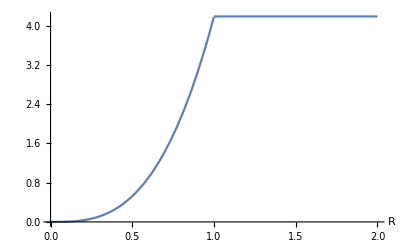

```mathematica
Block[
{p=1},
Plot[
norm A[R],{R,0,2p},
AxesLabel->Automatic
]
]
```